## Seasonal Ricker model - EWS in rnb - Singles

## Setup and Universal Parameters

```mathematica
(* set directory *)
SetDirectory["/Users/tbury/Google Drive/Research/doctorate/critical_transitions_18/ews_seasonal/models_ricker/ricker_seasonal_coe"];
```

```mathematica
(* Good fonts *)
TMBFS10={FontFamily->"Helvetica",FontSize->10};
TMBFS12={FontFamily->"Helvetica",FontSize->12};
TMBFS15={FontFamily->"Helvetica",FontSize->15};
TMBbold={FontFamily->"Helvetica",FontSize->15,Bold};
(* Neat colours *)
TMBcolours=ColorData[97,"ColorList"]
```

{RGBColor[0.368417, 0.506779, 0.709798],RGBColor[0.880722, 0.611041, 0.142051],RGBColor[0.560181, 0.691569, 0.194885],RGBColor[0.922526, 0.385626, 0.209179],RGBColor[0.528488, 0.470624, 0.701351],RGBColor[0.772079, 0.431554, 0.102387],RGBColor[0.363898, 0.618501, 0.782349],RGBColor[1, 0.75, 0],RGBColor[0.647624, 0.37816, 0.614037],RGBColor[0.571589, 0.586483, 0.],RGBColor[0.915, 0.3325, 0.2125],RGBColor[0.40082222609352647, 0.5220066643438841, 0.85],RGBColor[0.9728288904374106, 0.621644452187053, 0.07336199581899142],RGBColor[0.736782672705901, 0.358, 0.5030266573755369],RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}

```mathematica
(* system parameters *)
rw=0.4;
bl=-2.5;
bh=-0.0568;
```

## Import Data

```mathematica
(* Name of simluation run *)
simName="tmax400_rw0p4";
```

```mathematica
(* Import EWS DataFrame *)
dfEws=Import["data_export/trans_rnb/"<>simName<>"/ews_singles.csv"];
```

```mathematica
(* Import power spectrum DataFrame *)
dfPspec=Import["data_export/trans_rnb/"<>simName<>"/pspec.csv"];
```

```mathematica
(* Import ews means DataFrame *)
dfEwsMeans=Import["data_export/trans_rnb/"<>simName<>"/ews_means.csv"];
```

```mathematica
(* Import ews sd DataFrame *)
dfEwsSd=Import["data_export/trans_rnb/"<>simName<>"/ews_deviations.csv"];
```

```mathematica
(* Import Kendall tau values *)
dfKtau=Import["data_export/trans_rnb/"<>simName<>"/ktau.csv"];
```

```mathematica
numSims=Length[Union[dfEws[[2;;,1]]]]
```

10

```mathematica
(* Realisation number to display *)
displayNum=2;
```

## Figure params

```mathematica
(* Figure params *)
imgs=400; (* image size *)
aRatio=0.25; (* aspect ratio *)
aHeadSize=0.03;
{padLeft,padRight,padBottom,padTop}={30,5,5,5};  (* image padding *)
indexPos=Scaled[{0.065,1.11}]; (* scaled position of base index *)
labelPos=Scaled[{1.05,-0.1}]; (* scaled position of x label *)
arHeight=0.15; (* height of rolling window arrow *)
labelLetterPos=Scaled[{0.033,0.86}] ;(* panel letter label *)
labelLetterPosSize=12;
lt=0.0075; (* line thickness *)
ls=11; (* label style *)
ps=0.03; (* point size *)
font={FontFamily->"Helvetica",FontSize->16}; (* font format *)
textPos=Scaled[{0.03,0.12}]; (* position of text lablel *)
```

## Trajectory Plots

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* Extract info *)
realNum=1;
seriesB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Breeding",_,_}][[;;,{3,4}]];
seriesNB = Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Non-breeding",_,_}][[;;,{3,4}]];
(*seriesTotal= Cases[dfEws[[2;;,{1,2,3,4}]],{realNum,"Total",_,_}][[;;,{3,4}]];*)
```

```mathematica
(* Useful info *)
tVals=seriesB[[;;,1]];
tmax=tVals[[-1]];
dt2=tVals[[2]]-tVals[[1]];
windowComps=rw*tmax/dt2-1;
realMax=Max[dfEws[[;;,1]]][[1]];
stateVals=Union[dfEws[[2;;,2]]];
```

```mathematica
(* line legend *)
trajLegend=LineLegend[TMBcolours[[1;;2]],{"Breeding","Non-breeding"},Spacings->{0,0.2},LabelStyle->10]
```

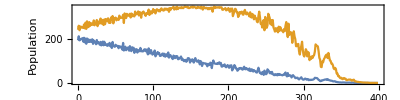

```mathematica
(* plot of breeding series *)
plotPop = ListPlot[{seriesB,seriesNB},
Joined->True,
LabelStyle->12,
PlotLegends->Placed[trajLegend,Scaled[{0.85,0.7}]],
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
AxesLabel->{"t","Population"},
PlotRange->{{0,tmax},All}]
```

### Output

```mathematica
rTicks=Range[bl,bh,0.2];
rTicksT=(rTicks-bh)*tmax/(bl-bh);
```

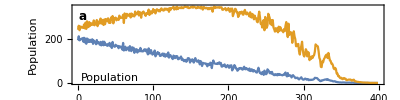

```mathematica
plotTraj=Show[{plotPop},
PlotRange->{{0,tmax*1.05},{-5,All}},
ImageSize->imgs,
LabelStyle->12,
AxesOrigin->{0,0},
Frame->{{True,True},{True,True}},
FrameLabel->{{None,None},{None,"Non-breeding growth rate, r_nb"}},
AspectRatio->aRatio,
ImagePadding->{{padLeft,padRight},{padBottom,40}},
FrameTicks->{{Automatic,Automatic},{Automatic,Transpose[{rTicksT,rTicks}]}},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0,FontSize->0],Automatic}},
Epilog->{Text[Style["a",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Population",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}]}
]
```

## EWS Plots (single realisations)

### Variance

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Variance"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

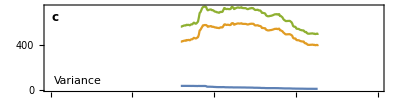

```mathematica
(* Plot EWS *)
plotVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Variance",ls],textPos,{-1,0}]}]
```

### Coefficient of variation

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Coefficient of variation"][[1,1]];
```

```mathematica
ewsVals=Table[Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}],{state,stateVals}][[;;,;;,{3,4}]];
```

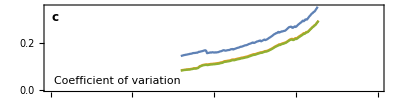

```mathematica
(* Plot EWS *)
plotCv=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Coefficient of variation",ls],textPos,{-1,0}]}]
```

### Smax/Var

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Smax/Var"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

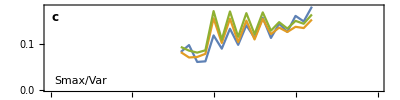

```mathematica
(* Plot EWS *)
plotSmaxVar=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Smax/Var",ls],textPos,{-1,0}]}]
```

### Skewness

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Skewness"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

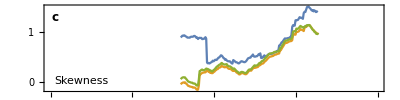

```mathematica
(* Plot EWS *)
plotSkew=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameTicksStyle->{{Automatic,Automatic},{Directive[FontOpacity->0],Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Skewness",ls],textPos,{-1,0}]}]
```

### Lag-1 AC

```mathematica
dfEws[[1]]
```

{Realisation number,Variable,Time,State variable,Smoothing,Residuals,Standard deviation,Variance,Lag-1 AC,Lag-2 AC,Lag-3 AC,Coefficient of variation,Skewness,Kurtosis,Smax,Smax/Var,Smax/Mean,Cross correlation}

```mathematica
(* relevant index in the DataFrame *)
indexEws=Position[dfEws[[1]],"Lag-1 AC"][[1,1]];
```

```mathematica
ewsVals=Table[DeleteCases[
Cases[dfEws[[2;;,{1,2,3,indexEws}]],{displayNum,state,_,_}][[;;,{3,4}]],
{_,""}],{state,stateVals}];
```

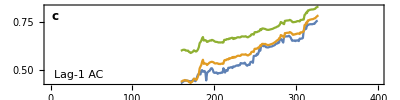

```mathematica
(* Plot EWS *)
plotAc1=ListPlot[ewsVals,
Joined->True,
ImageSize->imgs,
AspectRatio->aRatio,
LabelStyle->ls,
Frame->True,
Axes->False,
PlotRange->{{0,tmax},All},
FrameLabel->{{"",""},{"Time (arbitrary units)",""}},
FrameTicksStyle->{{Automatic,Automatic},{Automatic,Automatic}},
FrameTicks->{{Automatic,Automatic},{Automatic,Automatic}},
PlotRangeClipping->False, (* allows display of text outside of frame *)
ImagePadding->{{padLeft,padRight},{padBottom*10,padTop}},
Epilog->{Directive[{Black}],Arrowheads[{-aHeadSize,aHeadSize}],
(*Arrow[{Scaled[{0,arHeight},{0,ymin}],Scaled[{0,arHeight*2},{windowComps*dt2,ymin}]}]*)
(*Text[Style["×10^-2",14],indexPos]*)
Text[Style["c",labelLetterPosSize,Bold],labelLetterPos],
Text[Style["Lag-1 AC",ls],textPos,{-1,0}]}]
```

## Kendall Tau Plots

```mathematica
(* figure parameters *)
aRatioBox=1.5;
imgsBox=100;
padBox={{5,30},{5,5}};
ktauTextPos=Scaled[{0.05,0.12}];
ktauText=Text[Style["Kendall τ",ls],ktauTextPos,{-1,0}];
outliers=True;
labelLetterPosBox=Scaled[{0.07,0.86}];
```

### Variance

```mathematica
indexKtau=Position[dfKtau[[1]],"Variance"][[1,1]]
```

10

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.924862 | -0.973624 | -0.97896 | -0.981872 | -0.96961 | -0.973451 | -0.983716 | -0.970052 | -0.964234 | -0.950628 | -0.963865 | -0.896617 | -0.976608 | -0.987095 | -0.971041 | -0.972639 | -0.970003 | -0.980561 | -0.962394 | -0.961852 | -0.962421 | -0.966318 | -0.956299 | -0.950429 | -0.939588 | -0.959403 | -0.885737 | -0.964465 | -0.829402 | -0.959401 | -0.974723 | -0.985458 | -0.975567 | -0.95834 | -0.967141 | -0.968727 | -0.983317 | -0.971171 | -0.910364 | -0.971781 | -0.971673 | -0.958892 | -0.875729 | -0.96388 | -0.975848 | -0.985139 | -0.96225 | -0.971417 | -0.974132 | -0.982343 | -0.985404 | -0.98022 | -0.989419 | -0.979722 | -0.946637 | -0.977331 | -0.973482 | -0.969917 | -0.924113 | -0.976064 | -0.97666 | -0.964951 | -0.963751 | -0.966483 | -0.927874 | -0.955166 | -0.969273 | -0.959006 | -0.930464 | -0.896743 | -0.983907 | -0.965581 | -0.976972 | -0.982036 | -0.950437 | -0.969201 | -0.848304 | -0.945402 | -0.992905 | -0.961066 | -0.900928 | -0.898549 | -0.987209 | -0.873024 | -0.985743 | -0.945144 | -0.972558 | -0.984204 | -0.945452 | -0.978931 | -0.732031 | -0.941128 | -0.947512 | -0.984266 | -0.973007 | -0.951811 | -0.961151 | -0.977827 | -0.978164 | -0.98232
Non-breeding | 0.175885 | -0.283319 | -0.42453 | -0.152338 | 0.152928 | -0.210436 | -0.0448748 | -0.603618 | 0.0803277 | 0.34268 | 0.313875 | 0.0887013 | 0.0856793 | -0.386752 | -0.0951496 | -0.0854833 | -0.308718 | 0.02134 | -0.509614 | 0.0439628 | 0.315373 | -0.0269644 | 0.22403 | 0.156096 | 0.411303 | 0.0945683 | 0.0720134 | 0.216925 | 0.769473 | 0.0331145 | -0.227017 | -0.386353 | -0.00220779 | -0.180821 | -0.422264 | -0.104065 | -0.213636 | 0.0657237 | -0.254797 | -0.437855 | -0.348047 | 0.421441 | 0.135298 | 0.0537378 | -0.454352 | -0.534612 | -0.257665 | -0.464956 | -0.491347 | -0.169106 | -0.139483 | -0.644328 | -0.177847 | -0.236654 | 0.275794 | -0.525077 | -0.426881 | 0.0993238 | 0.0436887 | -0.181342 | -0.211664 | 0.141476 | -0.172375 | -0.239219 | 0.190919 | 0.316355 | -0.724173 | -0.21003 | 0.670357 | 0.143883 | -0.551265 | -0.106751 | -0.0653874 | -0.583404 | -0.0865232 | -0.126025 | 0.113833 | -0.0247875 | -0.677693 | -0.0878161 | -0.109445 | 0.0903178 | -0.672362 | 0.605437 | -0.473514 | 0.0643275 | -0.0798054 | -0.13353 | -0.195195 | -0.385404 | 0.352836 | 0.0457425 | 0.249261 | -0.456705 | -0.0810222 | -0.090471 | 0.297588 | -0.424754 | -0.190103 | -0.336873
Total | 0.15245 | -0.358411 | -0.515727 | -0.238701 | 0.0952748 | -0.285429 | -0.145017 | -0.642412 | 0.0204801 | 0.250383 | 0.171918 | 0.0449351 | -0.0631035 | -0.477377 | -0.191469 | -0.157035 | -0.418197 | -0.146402 | -0.53055 | -0.0332301 | 0.287888 | -0.170058 | 0.214359 | 0.0909091 | 0.334674 | 0.004489 | 0.0172097 | 0.0872671 | 0.699712 | 0.0120482 | -0.357722 | -0.47329 | -0.0485714 | -0.225462 | -0.470168 | -0.250111 | -0.261429 | -0.00810764 | -0.385002 | -0.535712 | -0.433488 | 0.363382 | 0.130018 | -0.031765 | -0.624857 | -0.598259 | -0.341459 | -0.487289 | -0.566849 | -0.411973 | -0.179357 | -0.672431 | -0.229446 | -0.286015 | 0.198248 | -0.690335 | -0.518456 | 0.000563539 | -0.00645248 | -0.226778 | -0.267526 | -0.0319602 | -0.424004 | -0.295587 | 0.128532 | 0.229637 | -0.765899 | -0.295299 | 0.642191 | 0.0324043 | -0.639725 | -0.186663 | -0.298879 | -0.645252 | -0.109503 | -0.246875 | 0.0339703 | -0.0851007 | -0.833662 | -0.131954 | -0.203211 | 0.0365115 | -0.79809 | 0.616765 | -0.584954 | -0.047678 | -0.144058 | -0.249413 | -0.270822 | -0.545807 | 0.311537 | 0.0370241 | 0.226141 | -0.643295 | -0.140344 | -0.117342 | 0.308352 | -0.467689 | -0.235016 | -0.519425

```mathematica
(* Box plot *)
boxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Skewness

```mathematica
indexKtau=Position[dfKtau[[1]],"Skewness"][[1,1]]
```

12

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.460405 | 0.346022 | 0.513281 | 0.477044 | 0.450909 | 0.0321045 | -0.526054 | -0.30298 | 0.297223 | -0.0273466 | 0.219841 | 0.891494 | -0.629033 | 0.19102 | 0.384337 | 0.645521 | 0.76333 | 0.397403 | 0.377609 | 0.762061 | 0.282233 | 0.204692 | 0.882583 | 0.630592 | 0.363442 | 0.0971749 | 0.523247 | 0.600157 | -0.206451 | 0.596057 | -0.542203 | 0.777778 | 0.179639 | 0.857867 | 0.324571 | -0.0781086 | 0.584105 | 0.0996803 | 0.04694 | 0.453416 | 0.656593 | 0.5559 | 0.725512 | -0.0365234 | 0.735153 | 0.531338 | 0.672958 | 0.380892 | -0.324612 | 0.391441 | 0.574534 | -0.0666437 | 0.76944 | 0.846154 | 0.132151 | 0.355004 | 0.792273 | 0.487311 | 0.692642 | 0.580443 | -0.319926 | 0.819058 | 0.646854 | 0.72018 | 0.780811 | 0.490179 | 0.734997 | 0.199534 | 0.339112 | 0.78908 | 0.782419 | 0.580952 | 0.560673 | 0.0199601 | -0.0121983 | 0.700395 | 0.956989 | 0.65663 | 0.524169 | 0.263305 | -0.502799 | 0.68966 | 0.276585 | 0.363179 | 0.409467 | 0.114514 | -0.0625949 | 0.491143 | 0.288421 | 0.438522 | 0.131864 | 0.784254 | 0.2746 | -0.762821 | 0.368984 | -0.347967 | -0.380427 | 0.358758 | 0.214227 | -0.515436
Non-breeding | 0.682715 | 0.781065 | 0.363004 | 0.496883 | 0.731638 | 0.718705 | 0.727161 | 0.373367 | 0.475367 | 0.160277 | 0.491874 | 0.903506 | -0.0946552 | 0.799083 | -0.0932233 | 0.891813 | 0.797906 | 0.818693 | 0.785982 | 0.935466 | 0.789907 | 0.610422 | 0.9488 | 0.709929 | -0.502682 | 0.888673 | 0.421777 | 0.882919 | 0.928403 | 0.622971 | 0.504199 | 0.907527 | 0.927273 | 0.900138 | 0.796696 | 0.454545 | 0.667792 | 0.43534 | 0.769585 | 0.313641 | 0.927877 | 0.197182 | 0.801105 | -0.136056 | 0.70423 | 0.653747 | 0.86428 | 0.885365 | 0.340051 | 0.288987 | 0.797101 | 0.63807 | 0.903681 | 0.895875 | 0.347207 | 0.800507 | 0.909552 | 0.809665 | 0.781422 | 0.857642 | 0.616943 | 0.85672 | 0.603453 | 0.73109 | 0.563939 | 0.593247 | 0.899791 | 0.732076 | 0.74728 | 0.894379 | 0.875982 | 0.743731 | 0.896477 | 0.696112 | 0.532153 | 0.739352 | 0.661114 | 0.769128 | 0.755531 | 0.857209 | -0.225176 | 0.659128 | 0.728643 | 0.726386 | 0.907298 | 0.270451 | 0.85336 | 0.653867 | 0.553656 | 0.671584 | 0.029777 | 0.831328 | 0.702726 | -0.0291188 | 0.929619 | 0.052647 | 0.640423 | 0.839503 | 0.896619 | 0.68813
Total | 0.688301 | 0.750634 | 0.291933 | 0.420909 | 0.763225 | 0.662104 | 0.676901 | 0.107739 | 0.517806 | 0.102008 | 0.131233 | 0.877403 | -0.193934 | 0.785263 | -0.127485 | 0.826109 | 0.813409 | 0.687179 | 0.776311 | 0.924045 | 0.81382 | 0.573697 | 0.947776 | 0.682782 | -0.499808 | 0.830765 | 0.242662 | 0.886646 | 0.909782 | 0.548806 | 0.490763 | 0.898549 | 0.93 | 0.894406 | 0.772599 | 0.275536 | 0.657013 | 0.305733 | 0.716464 | 0.436189 | 0.922041 | -0.0357355 | 0.802578 | -0.384922 | 0.679895 | 0.581939 | 0.829112 | 0.868615 | 0.368529 | 0.301404 | 0.832682 | 0.556832 | 0.890746 | 0.898877 | 0.32238 | 0.775148 | 0.909129 | 0.67512 | 0.752252 | 0.850518 | 0.608226 | 0.877354 | 0.631969 | 0.712887 | 0.526049 | 0.521968 | 0.892082 | 0.693582 | 0.743395 | 0.882286 | 0.886344 | 0.794654 | 0.900992 | 0.591857 | 0.592459 | 0.704323 | 0.728891 | 0.761432 | 0.685871 | 0.865878 | -0.349087 | 0.648485 | 0.697387 | 0.706169 | 0.854748 | 0.156244 | 0.786705 | 0.687495 | 0.487866 | 0.636957 | -0.0954661 | 0.824353 | 0.67133 | -0.442912 | 0.859405 | 0.07908 | 0.583416 | 0.800219 | 0.895803 | 0.635973

```mathematica
(* Box plot *)
boxSkew=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Coefficient of variation

```mathematica
indexKtau=Position[dfKtau[[1]],"Coefficient of variation"][[1,1]]
```

6

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.986495 | 0.95951 | 0.977216 | 0.910016 | 0.971169 | 0.933627 | 0.950766 | 0.920613 | 0.98275 | 0.952846 | 0.944563 | 0.900164 | 0.972618 | 0.969082 | 0.964636 | 0.959394 | 0.974407 | 0.96615 | 0.963314 | 0.976331 | 0.96761 | 0.972183 | 0.98137 | 0.935659 | 0.953963 | 0.965614 | 0.980074 | 0.983962 | 0.881914 | 0.987149 | 0.965706 | 0.967129 | 0.956388 | 0.978279 | 0.910916 | 0.948975 | 0.958095 | 0.980587 | 0.979628 | 0.885592 | 0.939559 | 0.96732 | 0.985227 | 0.922761 | 0.920099 | 0.926935 | 0.967899 | 0.941872 | 0.958463 | 0.921143 | 0.954969 | 0.924789 | 0.96937 | 0.967215 | 0.980636 | 0.938409 | 0.959224 | 0.966781 | 0.982048 | 0.969672 | 0.964246 | 0.956042 | 0.947991 | 0.948835 | 0.989082 | 0.972983 | 0.912741 | 0.956832 | 0.986014 | 0.984674 | 0.971342 | 0.959454 | 0.956884 | 0.957371 | 0.957884 | 0.977909 | 0.988089 | 0.948848 | 0.920916 | 0.952561 | 0.976689 | 0.975909 | 0.946297 | 0.966446 | 0.933134 | 0.934702 | 0.942201 | 0.965187 | 0.961947 | 0.913208 | 0.967583 | 0.990482 | 0.984054 | 0.927545 | 0.966556 | 0.98167 | 0.988574 | 0.922838 | 0.968734 | 0.94288
Non-breeding | 0.997571 | 0.997887 | 0.994825 | 0.986623 | 0.995763 | 0.98004 | 0.995654 | 0.972663 | 0.998976 | 0.994304 | 0.992924 | 0.985844 | 0.996464 | 0.997475 | 0.99367 | 0.992948 | 0.994016 | 0.991563 | 0.988622 | 0.994496 | 0.993944 | 0.996691 | 0.997724 | 0.991621 | 0.992912 | 0.995511 | 0.995322 | 0.998758 | 0.991083 | 0.997258 | 0.992552 | 0.992369 | 0.995974 | 0.992505 | 0.969555 | 0.996452 | 0.993896 | 0.99862 | 0.99514 | 0.978641 | 0.984438 | 0.996605 | 0.997176 | 0.996179 | 0.986445 | 0.99048 | 0.989335 | 0.982062 | 0.997079 | 0.986548 | 0.995399 | 0.992377 | 0.996147 | 0.994596 | 0.994889 | 0.992674 | 0.993519 | 0.995914 | 0.99758 | 0.995564 | 0.997545 | 0.995816 | 0.992426 | 0.985437 | 0.99804 | 0.99596 | 0.990281 | 0.992792 | 0.999417 | 0.997544 | 0.997055 | 0.994599 | 0.997742 | 0.989715 | 0.992763 | 0.995383 | 0.998857 | 0.993378 | 0.989047 | 0.98647 | 0.998637 | 0.998374 | 0.987538 | 0.998083 | 0.988588 | 0.993395 | 0.991113 | 0.997273 | 0.995969 | 0.99146 | 0.994763 | 0.998489 | 0.998555 | 0.989464 | 0.992627 | 0.998686 | 0.99907 | 0.985542 | 0.993794 | 0.984541
Total | 0.996357 | 0.99676 | 0.99402 | 0.981688 | 0.995249 | 0.97562 | 0.994709 | 0.96603 | 0.998521 | 0.99299 | 0.990713 | 0.975455 | 0.995648 | 0.998007 | 0.991469 | 0.989336 | 0.992112 | 0.989082 | 0.987143 | 0.992707 | 0.992547 | 0.997022 | 0.997383 | 0.988437 | 0.991571 | 0.995212 | 0.993985 | 0.997981 | 0.985313 | 0.99697 | 0.990654 | 0.99192 | 0.995195 | 0.991292 | 0.965803 | 0.995713 | 0.991688 | 0.998505 | 0.994973 | 0.972128 | 0.980398 | 0.996605 | 0.996562 | 0.992517 | 0.979912 | 0.98572 | 0.987431 | 0.976004 | 0.995619 | 0.983444 | 0.994939 | 0.990898 | 0.994496 | 0.993995 | 0.994012 | 0.989856 | 0.992392 | 0.994224 | 0.997311 | 0.994892 | 0.996562 | 0.994228 | 0.990309 | 0.98142 | 0.997387 | 0.993651 | 0.986426 | 0.991565 | 0.999223 | 0.997544 | 0.997055 | 0.994048 | 0.995969 | 0.987884 | 0.99124 | 0.995223 | 0.99853 | 0.99123 | 0.985834 | 0.98358 | 0.998031 | 0.998226 | 0.984422 | 0.996166 | 0.985207 | 0.99023 | 0.988471 | 0.997728 | 0.994034 | 0.990528 | 0.994763 | 0.997908 | 0.998292 | 0.987356 | 0.991119 | 0.998101 | 0.999336 | 0.98306 | 0.992324 | 0.977282

```mathematica
(* Box plot *)
boxCv=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax"][[1,1]]
```

13

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | -0.590643 | -0.588235 | -0.766082 | -0.581699 | -0.607843 | -0.647059 | -0.733333 | -0.473684 | -0.426901 | -0.867647 | -0.604396 | -0.346405 | -0.856209 | -0.699346 | -0.720588 | -0.583333 | -0.79085 | -0.733333 | -0.80117 | -0.544118 | -0.616667 | -0.8 | -0.0292398 | -0.766667 | -0.12381 | -0.808824 | -0.28655 | -0.8 | -0.410256 | 0.294118 | -0.735294 | -0.838235 | -0.699346 | -0.614035 | -0.808824 | -0.779412 | -0.568627 | -0.403509 | -0.433333 | -0.808824 | -0.926471 | -0.866667 | -0.490196 | -0.816667 | -0.833333 | -0.830065 | -0.816993 | -0.497076 | -0.838235 | -0.764706 | -0.926471 | -0.871345 | -0.867647 | -0.695906 | -0.0147059 | -0.838235 | -0.867647 | -0.838235 | -0.581699 | -0.830065 | -0.542484 | -0.75 | -0.730994 | -0.411765 | -0.366667 | -0.75 | -0.866667 | -0.823529 | -0.580952 | -0.885714 | -0.873684 | -0.918129 | -0.816667 | -0.691176 | -0.777778 | -0.833333 | -0.7 | -0.00952381 | -0.867647 | -0.751634 | -0.75 | -0.470588 | -0.842105 | -0.266667 | -0.852941 | -0.647059 | -0.80117 | -0.735294 | -0.65 | -0.816667 | -0.132353 | -0.0994152 | -0.372549 | -0.885714 | -0.35 | -0.647059 | -0.45098 | -0.647059 | -0.85 | -0.607843
Non-breeding | 0.578947 | 0.220588 | 0.251462 | 0.0196078 | 0.372549 | -0.25 | 0.485714 | -0.178947 | 0.450292 | 0.779412 | 0.538462 | 0.633987 | 0.764706 | 0.607843 | 0.294118 | -0.116667 | -0.0588235 | 0.133333 | -0.239766 | 0.464052 | 0.705882 | -0.05 | 0.532164 | 0.55 | 0.657143 | 0.647059 | 0.204678 | 0.632353 | 0.717949 | 0.573529 | -0.308824 | 0.161765 | 0.281046 | -0.0210526 | -0.0735294 | 0.470588 | 0.372549 | 0.555556 | 0.433333 | -0.411765 | -0.455882 | 0.7 | 0.321637 | 0.85 | 0.316667 | -0.385621 | 0.150327 | -0.263158 | -0.367647 | -0.0147059 | -0.235294 | 0.450292 | 0.477124 | 0.391813 | 0.411765 | -0.102941 | -0.205882 | 0.455882 | -0.0588235 | 0.45098 | 0.274854 | 0.602941 | 0.438596 | 0.333333 | 0.666667 | 0.514706 | -0.266667 | 0.588235 | 0.828571 | 0.295238 | -0.463158 | 0.442105 | 0.416667 | -0.132353 | 0.385621 | 0.816667 | 0.683333 | 0.695238 | -0.382353 | 0.111111 | 0.558824 | 0.397059 | -0.168421 | 0.683333 | -0.117647 | 0.189542 | 0.309942 | 0.691176 | -0.0333333 | 0.426471 | 0.558824 | 0.438596 | 0.320261 | -0.180952 | 0.316667 | 0.455882 | 0.712418 | -0.147059 | 0.566667 | 0.124183
Total | 0.555556 | 0.147059 | 0.00584795 | -0.0196078 | 0.228758 | -0.294118 | 0.466667 | -0.221053 | 0.333333 | 0.617647 | 0.428571 | 0.542484 | 0.764706 | 0.529412 | 0.176471 | -0.25 | -0.163399 | -0.0833333 | -0.380117 | 0.424837 | 0.647059 | -0.266667 | 0.497076 | 0.433333 | 0.52381 | 0.544118 | 0.146199 | 0.529412 | 0.589744 | 0.529412 | -0.367647 | -0.102941 | 0.202614 | -0.105263 | -0.220588 | 0.117647 | 0.254902 | 0.520468 | 0.333333 | -0.676471 | -0.691176 | 0.483333 | 0.263158 | 0.733333 | -0.0333333 | -0.464052 | 0.0326797 | -0.298246 | -0.544118 | -0.205882 | -0.294118 | 0.321637 | -0.0196078 | 0.274854 | 0.382353 | -0.5 | -0.323529 | 0.397059 | -0.111111 | 0.0588235 | 0.216374 | 0.455882 | 0.356725 | 0.24183 | 0.566667 | 0.352941 | -0.433333 | 0.338235 | 0.733333 | 0.180952 | -0.578947 | 0.231579 | 0.2 | -0.279412 | 0.176471 | 0.766667 | 0.533333 | 0.619048 | -0.573529 | -0.254902 | 0.514706 | 0.264706 | -0.252632 | 0.616667 | -0.5 | 0.0457516 | 0.22807 | 0.661765 | -0.15 | -0.0441176 | 0.5 | 0.415205 | 0.228758 | -0.352381 | 0.266667 | 0.397059 | 0.699346 | -0.147059 | 0.55 | 0.0326797

```mathematica
(* Box plot *)
boxSmax=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Smax/Var

```mathematica
indexKtau=Position[dfKtau[[1]],"Smax/Var"][[1,1]]
```

8

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.80117 | 0.676471 | 0.520468 | 0.464052 | 0.503268 | -0.0882353 | 0.485714 | 0.252632 | 0.824561 | 0.235294 | 0.384615 | 0.686275 | 0.79085 | 0.660131 | 0.191176 | 0.166667 | 0.424837 | 0.25 | 0.532164 | 0.838235 | 0.766667 | -0.116667 | 0.625731 | 0.566667 | 0.790476 | 0.808824 | 0.309942 | 0.5 | 0.307692 | 0.838235 | -0.220588 | 0.25 | 0.764706 | 0.497076 | 0.632353 | 0.441176 | 0.830065 | 0.80117 | 0.8 | 0.161765 | -0.25 | 0.0333333 | 0.464052 | 0.35 | 0.25 | 0.215686 | 0.477124 | 0.567251 | 0.25 | 0.382353 | 0.588235 | 0.777778 | 0.323529 | 0.847953 | 0.720588 | 0.25 | 0.382353 | 0.455882 | 0.176471 | 0.503268 | 0.803922 | 0.323529 | 0.567251 | 0.699346 | 0.733333 | -0.0588235 | 0.616667 | 0.544118 | 0.542857 | 0.371429 | 0.421053 | 0.555556 | 0.533333 | 0.617647 | 0.764706 | 0.833333 | 0.833333 | 0.847619 | 0.161765 | 0.0849673 | 0.632353 | 0.588235 | 0.589474 | 0.733333 | 0.161765 | 0.647059 | 0.812865 | 0.676471 | 0. | 0.4 | 0.544118 | 0.824561 | 0.594771 | 0.485714 | 0.733333 | 0.720588 | 0.568627 | 0.691176 | 0.666667 | 0.568627
Non-breeding | 0.707602 | 0.411765 | 0.649123 | 0.150327 | 0.411765 | -0.367647 | 0.695238 | 0.105263 | 0.789474 | 0.632353 | 0.56044 | 0.699346 | 0.751634 | 0.79085 | 0.594771 | -0.283333 | 0.202614 | 0.283333 | 0.251462 | 0.803922 | 0.705882 | -0.183333 | 0.54386 | 0.583333 | 0.504762 | 0.75 | 0.204678 | 0.647059 | 0.358974 | 0.838235 | -0.382353 | 0.382353 | 0.633987 | 0.568421 | 0.676471 | 0.661765 | 0.660131 | 0.847953 | 0.666667 | -0.0441176 | -0.0735294 | 0.333333 | 0.415205 | 0.783333 | 0.55 | 0.45098 | 0.607843 | 0.426901 | 0.176471 | 0.352941 | 0.308824 | 0.836257 | 0.581699 | 0.836257 | 0.470588 | 0.602941 | 0.147059 | 0.514706 | -0.0588235 | 0.581699 | 0.730994 | 0.308824 | 0.660819 | 0.738562 | 0.75 | 0.279412 | 0.6 | 0.558824 | 0.409524 | 0.104762 | 0.0315789 | 0.684211 | 0.383333 | 0.617647 | 0.607843 | 0.783333 | 0.816667 | 0.828571 | 0.352941 | 0.189542 | 0.75 | 0.352941 | 0.536842 | 0.683333 | 0.485294 | 0.411765 | 0.707602 | 0.882353 | -0.0666667 | 0.647059 | 0.661765 | 0.672515 | 0.281046 | 0.428571 | 0.666667 | 0.779412 | 0.699346 | 0.647059 | 0.516667 | 0.333333
Total | 0.649123 | 0.382353 | 0.602339 | 0.0718954 | 0.333333 | -0.382353 | 0.638095 | 0.0947368 | 0.719298 | 0.470588 | 0.494505 | 0.699346 | 0.72549 | 0.764706 | 0.477124 | -0.333333 | 0.124183 | 0.05 | -0.0877193 | 0.79085 | 0.617647 | -0.466667 | 0.508772 | 0.533333 | 0.504762 | 0.691176 | 0.122807 | 0.602941 | 0.25641 | 0.808824 | -0.470588 | 0.294118 | 0.555556 | 0.463158 | 0.588235 | 0.367647 | 0.673203 | 0.812865 | 0.65 | -0.367647 | -0.279412 | 0.116667 | 0.28655 | 0.683333 | 0.416667 | 0.333333 | 0.490196 | 0.356725 | -0.117647 | 0.279412 | 0.235294 | 0.80117 | 0.477124 | 0.777778 | 0.441176 | 0.455882 | 0.0588235 | 0.352941 | -0.202614 | 0.424837 | 0.684211 | 0.191176 | 0.602339 | 0.738562 | 0.683333 | 0.147059 | 0.55 | 0.455882 | 0.0857143 | -0.12381 | -0.126316 | 0.547368 | 0.316667 | 0.544118 | 0.51634 | 0.833333 | 0.75 | 0.828571 | 0.176471 | 0.124183 | 0.735294 | 0.264706 | 0.515789 | 0.55 | 0.352941 | 0.385621 | 0.707602 | 0.808824 | -0.3 | 0.676471 | 0.617647 | 0.625731 | 0.111111 | 0.371429 | 0.616667 | 0.75 | 0.607843 | 0.573529 | 0.55 | 0.294118

```mathematica
(* Box plot *)
boxSmaxVar=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

### Lag-1 Autocorrelation

```mathematica
indexKtau=Position[dfKtau[[1]],"Lag-1 AC"][[1,1]]
```

4

```mathematica
ktauVals=
Table[Prepend[Cases[dfKtau[[2;;,{2,indexKtau}]],{state,_}][[;;,2]],state],{state,stateVals}];
```

```mathematica
ktauVals//TableForm
```

Breeding | 0.923143 | 0.897776 | 0.761232 | 0.833169 | 0.926364 | 0.544189 | 0.912261 | 0.554033 | 0.915359 | 0.895935 | 0.695657 | 0.857603 | 0.923082 | 0.947036 | 0.831813 | 0.670791 | 0.897076 | 0.786678 | 0.894198 | 0.867873 | 0.916667 | 0.859238 | 0.964119 | 0.922757 | 0.848679 | 0.876846 | 0.885849 | 0.812893 | 0.513261 | 0.967287 | 0.769254 | 0.702037 | 0.927094 | 0.910554 | 0.75743 | 0.837348 | 0.939836 | 0.932578 | 0.930906 | 0.890499 | 0.601303 | 0.75903 | 0.963998 | 0.804241 | 0.599173 | 0.644857 | 0.82717 | 0.70672 | 0.862971 | 0.902738 | 0.813509 | 0.918924 | 0.74048 | 0.910874 | 0.927273 | 0.657827 | 0.903479 | 0.896493 | 0.955936 | 0.94764 | 0.883551 | 0.91559 | 0.699201 | 0.768933 | 0.910505 | 0.910624 | 0.822256 | 0.950466 | 0.930661 | 0.925862 | 0.854616 | 0.930159 | 0.734444 | 0.793841 | 0.846045 | 0.832782 | 0.967577 | 0.903138 | -0.0645972 | 0.811973 | 0.856146 | 0.888074 | 0.67423 | 0.916821 | 0.520103 | 0.895023 | 0.866189 | 0.782839 | 0.498775 | 0.526101 | 0.901538 | 0.932785 | 0.95389 | 0.273699 | 0.796112 | 0.944124 | 0.961151 | 0.787288 | 0.906865 | 0.842377
Non-breeding | 0.933459 | 0.925472 | 0.848082 | 0.871948 | 0.934001 | 0.62917 | 0.898725 | 0.578191 | 0.96325 | 0.939102 | 0.805417 | 0.922468 | 0.898817 | 0.977011 | 0.854833 | 0.690918 | 0.917449 | 0.825972 | 0.935146 | 0.891572 | 0.953727 | 0.895616 | 0.971442 | 0.937495 | 0.808046 | 0.923388 | 0.91902 | 0.935714 | 0.609756 | 0.975326 | 0.8341 | 0.766273 | 0.951039 | 0.9159 | 0.861338 | 0.911899 | 0.948831 | 0.949629 | 0.886552 | 0.914868 | 0.751758 | 0.925473 | 0.967096 | 0.94475 | 0.641516 | 0.805522 | 0.891195 | 0.735091 | 0.912231 | 0.948559 | 0.835595 | 0.941973 | 0.857723 | 0.949318 | 0.926543 | 0.845027 | 0.9459 | 0.936179 | 0.953354 | 0.968679 | 0.929527 | 0.917755 | 0.879142 | 0.749294 | 0.958354 | 0.952529 | 0.87499 | 0.96534 | 0.924242 | 0.953141 | 0.863656 | 0.927914 | 0.870354 | 0.826289 | 0.864915 | 0.972932 | 0.972562 | 0.957226 | 0.717269 | 0.848801 | 0.918503 | 0.947524 | 0.64804 | 0.961659 | 0.658495 | 0.885243 | 0.911007 | 0.931682 | 0.751028 | 0.686801 | 0.902589 | 0.94862 | 0.971363 | 0.276437 | 0.806954 | 0.96057 | 0.97648 | 0.797444 | 0.927813 | 0.825649
Total | 0.919373 | 0.894336 | 0.73699 | 0.820779 | 0.926425 | 0.382806 | 0.809164 | 0.492362 | 0.945272 | 0.901862 | 0.687783 | 0.904156 | 0.877057 | 0.967311 | 0.823598 | 0.645855 | 0.894601 | 0.732672 | 0.910229 | 0.85442 | 0.947826 | 0.839868 | 0.962567 | 0.929786 | 0.671648 | 0.889421 | 0.890281 | 0.866149 | 0.518752 | 0.96537 | 0.623366 | 0.680383 | 0.931948 | 0.896941 | 0.757882 | 0.832964 | 0.932857 | 0.932494 | 0.832761 | 0.82716 | 0.624719 | 0.787624 | 0.963536 | 0.925165 | 0.33758 | 0.734938 | 0.833936 | 0.654669 | 0.862139 | 0.917221 | 0.831455 | 0.940494 | 0.791538 | 0.924818 | 0.909748 | 0.715976 | 0.934207 | 0.911243 | 0.934669 | 0.950397 | 0.919583 | 0.88832 | 0.719855 | 0.67196 | 0.945125 | 0.909675 | 0.788354 | 0.943869 | 0.913753 | 0.930846 | 0.776832 | 0.889997 | 0.75006 | 0.637926 | 0.807275 | 0.954781 | 0.96652 | 0.93038 | 0.206718 | 0.78509 | 0.878209 | 0.936142 | 0.610151 | 0.93848 | 0.36785 | 0.865291 | 0.870174 | 0.893509 | 0.557204 | 0.559783 | 0.871615 | 0.94025 | 0.967028 | -0.254981 | 0.715794 | 0.95356 | 0.971298 | 0.751004 | 0.901682 | 0.76314

```mathematica
(* Box plot *)
boxAc1=BoxWhiskerChart[ktauVals[[;;,2;;]],If[outliers,{{"Outliers","•"},{"FarOutliers","•"}}],
LabelStyle->ls,
PlotRange->{-1,1},
Frame->True,
AspectRatio->aRatio*(imgs/imgsBox),
FrameTicks->{{None,Range[-1,1,0.5]},{Automatic,Automatic}},
FrameTicksStyle->{{Directive[FontOpacity->0],{True,Directive[FontOpacity->1]}},{None,None}},
ChartStyle->TMBcolours[[1;;3]],
ImageSize->imgsBox,
ImagePadding->padBox,
Epilog->{
ktauText,
Text[Style["d",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

-Graphics-

## Power Spectrum Plot

### Colour function

```mathematica
colFun1[z_]:=Blend[{Blue,Orange},z]
```

```mathematica
Table[colFun1[i],{i,0,1,0.1}]
```

{RGBColor[0., 0., 1.],RGBColor[0.1, 0.05, 0.9],RGBColor[0.2, 0.1, 0.8],RGBColor[0.30000000000000004, 0.15000000000000002, 0.7],RGBColor[0.4, 0.2, 0.6],RGBColor[0.5, 0.25, 0.5],RGBColor[0.6000000000000001, 0.30000000000000004, 0.3999999999999999],RGBColor[0.7000000000000001, 0.35000000000000003, 0.29999999999999993],RGBColor[0.8, 0.4, 0.19999999999999996],RGBColor[0.9, 0.45, 0.09999999999999998],RGBColor[1., 0.5, 0.]}

### Organise power spectrum data

```mathematica
(* time values to plot power spectrum *)
plotTimes = Union[dfPspec[[2;;,3]]][[1;;-1;;7]]
```

{159.,229.,299.}

```mathematica
Round[plotTimes]
```

{159,229,299}

```mathematica
dfPspec[[1]]
```

{Realisation number,Variable,Time,Frequency,Empirical}

```mathematica
(* Power spectra of display plot *)
specData=Table[
Cases[dfPspec,{displayNum,"Total",timeVal,_,_}][[;;,{4,5}]],
{timeVal,plotTimes}];
```

```mathematica
(* Power spectra normalised by the variance *)
varianceVals=Table[Cases[dfEws[[2;;,{1,2,3,8}]],{displayNum,"Total",Round[time],_}][[1,4]],{time,plotTimes}];
specNormData=specData;
specNormData[[;;,;;,2]]=specNormData[[;;,;;,2]]/varianceVals;
```

```mathematica
(* normalise color map - each trajectory is mapped to a color *)
plotTimesUnit=(plotTimes-plotTimes[[1]])/(plotTimes[[-1]]-plotTimes[[1]]);
```

```mathematica
(* line legend *)
lineLegend=LineLegend[colFun1[#]&/@plotTimesUnit,Style["t="<>ToString[#],(ls-1)]&/@Round[plotTimes+1],Spacings->{0,0.2}]
```

```mathematica
specData//Dimensions
```

{3,41,2}

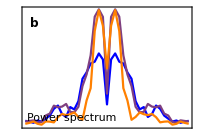

```mathematica
plotPspec=ListLinePlot[specData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

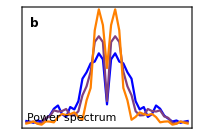

```mathematica
plotPspecNorm=ListLinePlot[specNormData,
PlotRange->All,
PlotStyle->Thread@{colFun1[#]&/@plotTimesUnit},
LabelStyle->ls,
Frame->True,
AxesOrigin->{0,0},
Axes->{False,False},
ImagePadding->{{5,6*padRight},{padBottom,40}},
ImageSize->200,
AspectRatio->0.7,
FrameLabel->{{None,None},{None,"Frequency, ω"}},
PlotRangeClipping->False,
FrameTicks->{{None,Automatic},{None,Range[-4,4,1]}},
PlotLegends->Placed[lineLegend,Scaled[{0.8,0.7}]],
Epilog->{
Text[Style["Power spectrum",ls],Scaled[{textPos[[1,1]],textPos[[1,2]]*0.7}],{-1,0}],
Text[Style["b",labelLetterPosSize,Bold],labelLetterPosBox]}]
```

## Grid Plot

```mathematica
cm=72/2.54;
```

### Dimensions of Plot

```mathematica
(* Horizontal dimensions *)
leftPad=1.2cm;
widthEws=12.05cm;
widthBox=5cm;
rightPad=1.2cm;
(* Total horizontal dimension *)
imWidth=leftPad+widthEws+widthBox+rightPad;

(* Vertical dimensions *)
bottomPad=1.2cm;
heightEws=2.5cm;
heightBif=3.5cm;
gapVert=0.5cm;
topPad=1.5cm;
(* Total vertical dimension *)
imHeight=bottomPad+4*heightEws+heightBif+4*gapVert+topPad;
```

### Construct grid plot

```mathematica
plotGrid=Graphics[{
(* 1st (bottom) row *)
Inset[Show[plotAc1,AspectRatio->Full,ImagePadding->{{leftPad,0},{bottomPad,0}}],{0,0},{Left,Bottom},{widthEws+leftPad,heightEws+bottomPad}],
Inset[Show[boxAc1,AspectRatio->Full,ImagePadding->{{0,rightPad},{bottomPad,0}}],{widthEws+leftPad,0},{Left,Bottom},{widthBox+rightPad,heightEws+bottomPad}],
(* 2nd row *)
Inset[Show[plotSmaxVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+heightEws+gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxSmaxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+heightEws+gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 3rd row *)
Inset[Show[plotCv,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxCv,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+2*heightEws+2*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 4th row *)
Inset[Show[plotVar,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,0}}],{0,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthEws+leftPad,heightEws}],
Inset[Show[boxVar,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,0}}],{leftPad+widthEws,bottomPad+3*heightEws+3*gapVert},{Left,Bottom},{widthBox+rightPad,heightEws}],
(* 5th (top) row  *)
Inset[Show[plotTraj,AspectRatio->Full,ImagePadding->{{leftPad,0},{1,topPad}}],{0,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthEws+leftPad,heightBif+topPad}],
Inset[Show[plotPspecNorm,AspectRatio->Full,ImagePadding->{{0,rightPad},{1,topPad}}],{leftPad+widthEws,bottomPad+4*heightEws+4*gapVert},{Left,Bottom},{widthBox+rightPad,heightBif+topPad}]
},
ImageSize->{imWidth,imHeight}];
```

### Export plot

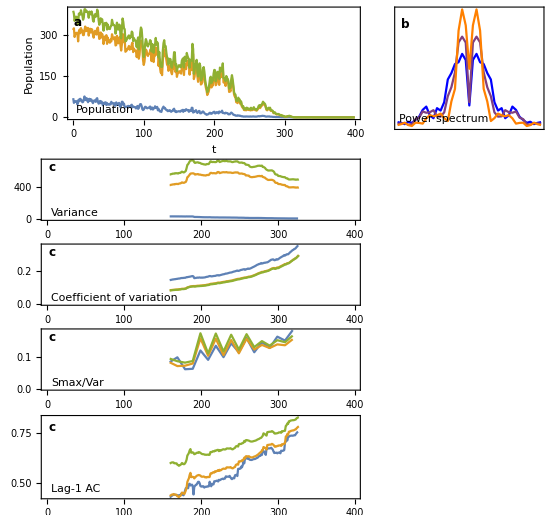

```mathematica
plotGrid
```

```mathematica
Export["figures/singles_"<>simName<>".png",plotGrid,ImageResolution->200];
```